```mathematica
data = SemanticImport["C:\\Users\\peter-mueller\\Documents\\hm-ss17\\modellbildung\\2017-koester-modellbildung\\Studienarbeit_1\\Daten2012\\MessexperimentGeschwindigkeitenSS2012.csv"]
```

Dataset[<>]

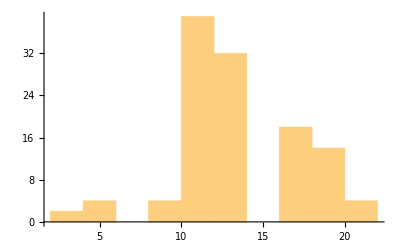

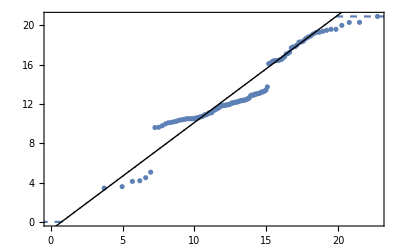

```mathematica
zeiten = data[All, "Zeit in sec"];
Histogram[zeiten]
QuantilePlot@zeiten
```

```mathematica
a = Values@Normal@data[All,{"Runde","Zeit in sec"}];
LinearModelFit[a, x,x]
```

FittedModel[13.111+0.0547436 x]